# Parameter-Robustness of our 4 illustrative simulation runs

This notebook checks parameter robustness of our simulation results, using the ensemble “2020_06_25-0001” with randomly chosen weights of the achievement function.

```mathematica
SetDirectory[$HomeDirectory];
If[!MemberQ[$Path,#],AppendTo[$Path, #]]&[FileNameJoin[{"git","remoma","packages","DialecticalStructures"}]];
If[!MemberQ[$Path,#],AppendTo[$Path, #]]&[FileNameJoin[{"git","remoma","packages","ReflectiveEquilibrium"}]];
<<DialecticalStructures`BasicTDS`;
<<DialecticalStructures`InductiveReasoning`;
<<DialecticalStructures`PositionsAnalytics`;
<<ReflectiveEquilibrium`ReflectiveEquilibrium`;
```

## Setting up the scene

```mathematica
ensembleDir="par-narrow_sample";
fileRoot="2020_06_26-0001";
fourCasesDir="four_cases";
fourCasesRoot="2016_09_08-0001";
```

Get data from first case.

```mathematica
data=Get[FileNameJoin[{
NotebookDirectory[],
"..","results",
ensembleDir, 
fileRoot<>"#"<>IntegerString[1,10,6]<>".m"
}]];
senIDs=Cases[data,{"senIDs",_}][[1,2]];  
tau=Cases[data,{"tau",_}][[1,2]];  param=Cases[data,{"parameters",_}][[1,2]];
```

Gather the ensemble data according to initial commitments.

```mathematica
ensembleDataSplit=GatherBy[
Module[{
n
},
n=Length[FileNames[fileRoot<>"#*.m",FileNameJoin[{
NotebookDirectory[],
"..","results",
ensembleDir}]]];
Table[
Get[FileNameJoin[{
NotebookDirectory[],
"..","results",
ensembleDir, 
fileRoot<>"#"<>IntegerString[i,10,6]<>".m"
}]],
{i,n}
]
],
Lookup[Part[Cases[#,{"posEvolution",_}],1,2,1],"COM"]&
];
```

Get the position-evolutions for four cases

```mathematica
posEvolFourCases=Module[{
n,pe
},
n=Length[FileNames[fourCasesRoot<>"#*.m",FileNameJoin[{
NotebookDirectory[],
"..","results",
fourCasesDir}]]];
Echo@n;
Association@Table[
pe=Cases[
Get[FileNameJoin[{
NotebookDirectory[],
"..","results",
fourCasesDir, 
fourCasesRoot<>"#"<>IntegerString[i,10,6]<>".m"
}]],
{"posEvolution",_}];
Echo@pe;
Lookup[Part[pe,1,2,1],"COM"]->pe,
{i,n}
]
]
```

4

{{posEvolution,{<|THE→1,COM→118|>,<|THE→611,COM→611|>,<|THE→611,COM→611|>}}}

{{posEvolution,{<|THE→1,COM→121|>,<|THE→611,COM→611|>,<|THE→611,COM→611|>}}}

{{posEvolution,{<|THE→1,COM→1090|>,<|THE→1122,COM→1122|>,<|THE→1113,COM→1113|>,<|THE→1113,COM→1113|>}}}

{{posEvolution,{<|THE→1,COM→1333|>,<|THE→1340,COM→1340|>,<|THE→611,COM→611|>,<|THE→611,COM→611|>}}}

<|118→{{posEvolution,{<|THE→1,COM→118|>,<|THE→611,COM→611|>,<|THE→611,COM→611|>}}},121→{{posEvolution,{<|THE→1,COM→121|>,<|THE→611,COM→611|>,<|THE→611,COM→611|>}}},1090→{{posEvolution,{<|THE→1,COM→1090|>,<|THE→1122,COM→1122|>,<|THE→1113,COM→1113|>,<|THE→1113,COM→1113|>}}},1333→{{posEvolution,{<|THE→1,COM→1333|>,<|THE→1340,COM→1340|>,<|THE→611,COM→611|>,<|THE→611,COM→611|>}}}|>

```mathematica
Lookup[posEvolFourCases,118]
```

{{posEvolution,{<|THE→1,COM→118|>,<|THE→611,COM→611|>,<|THE→611,COM→611|>}}}

Functions to calculate weights given parameters alpha and beta of simulation

```mathematica
WeightAccount[alpha_,beta_]:=(alpha*beta)/(alpha+beta-alpha*beta);
WeightSystematicity[alpha_,beta_]:=(beta-alpha*beta)/(alpha+beta-alpha*beta);
WeightCloseness[alpha_,beta_]:=1-(WeightAccount[alpha,beta]+WeightSystematicity[alpha,beta]);
```

```mathematica
PlotData[ensembleData_]:=Module[{alpha,beta, posevol,matchesStandardCaseQ},
Map[
Function[
data,
alpha=Lookup[
Cases[data,{"parameters",_}][[1,2]],
"alpha"];
PrintTemporary["  alpha: "<>ToString[alpha]];

beta=Lookup[
Cases[data,{"parameters",_}][[1,2]],
"beta"];
PrintTemporary["  beta: "<>ToString[beta]];

matchesStandardCaseQ=Equal[
Cases[data,{"posEvolution",_}],
Lookup[
posEvolFourCases,
Lookup[Part[Cases[data,{"posEvolution",_}],1,2,1],"COM"]
]
];

Style[
{WeightSystematicity[alpha,beta],WeightAccount[alpha,beta]},
If[matchesStandardCaseQ,Red,Blue]
]
],
ensembleData
]
];
```

```mathematica
PlotData@((ensembleDataSplit[[4]])[[1;;10]])
```

{{0.513967,0.397618},{0.609296,0.288997},{0.504997,0.463265},{0.449624,0.381943},{0.532111,0.315632},{0.6529,0.342015},{0.409548,0.358884},{0.51422,0.430526},{0.505138,0.326844},{0.517482,0.314966}}

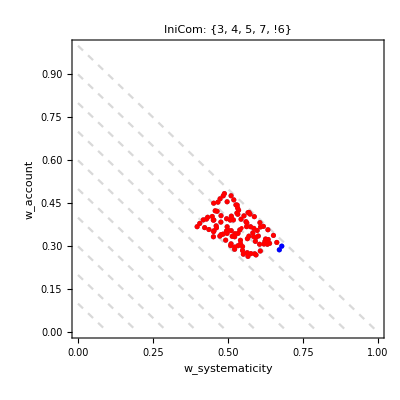
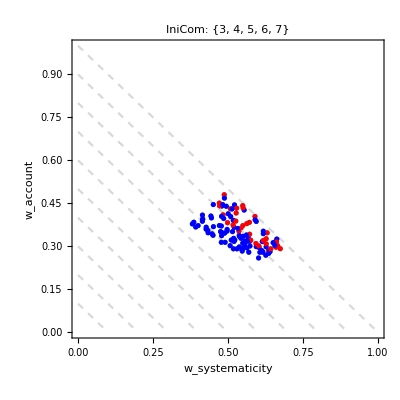
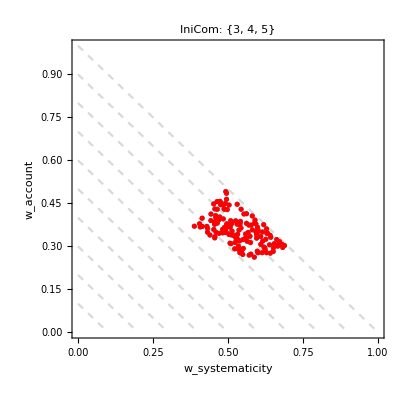
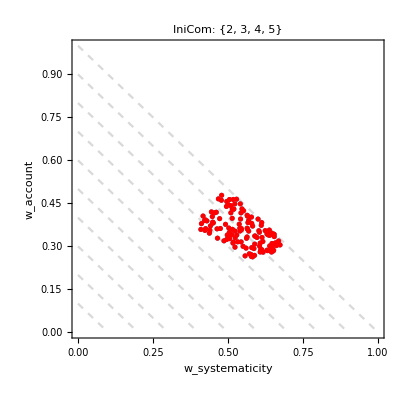

```mathematica
With[{wa=0.36363636363636365,ws=0.5454545454545454},
Map[
Function[
splitDataRecords,
Show[
Table[
Plot[-x+c,{x,0,1},
PlotStyle->{Dashed,LightGray},
PlotLabel->"IniCom: "<>ToString[IntegerToList[Lookup[Part[Cases[First@splitDataRecords,{"posEvolution",_}],1,2,1],"COM"],senIDs]],
Frame->True,
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
FrameLabel->{"w_systematicity","w_account"}
],
{c,0,1,0.1}
],
ListPlot[PlotData@splitDataRecords],
Graphics[{Red,PointSize[Large],Point[{ws,wa}]}]
]
],
ensembleDataSplit
]
]
```

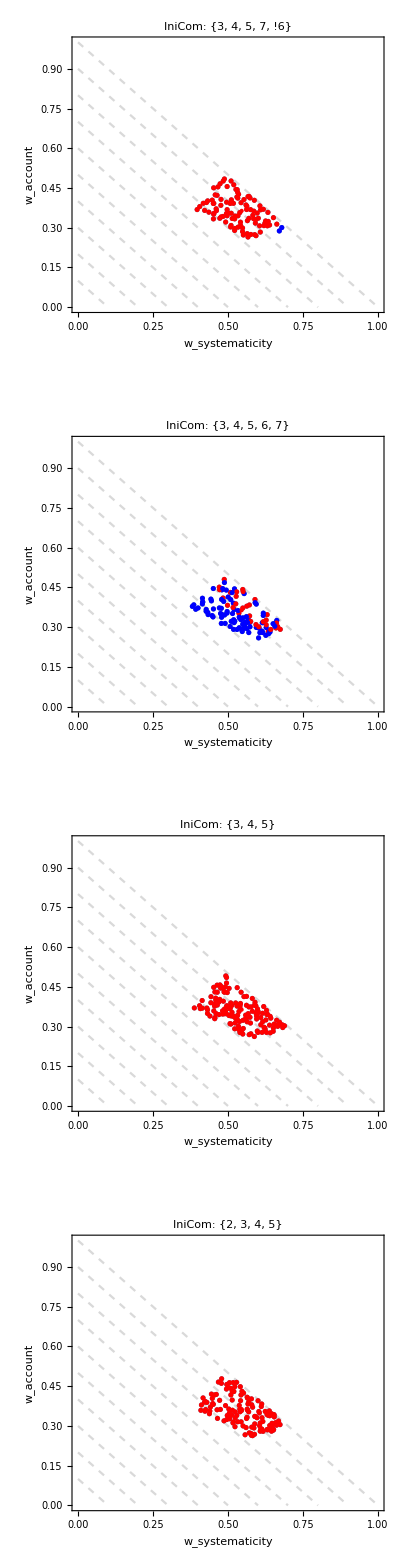

```mathematica
GraphicsColumn[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},ImageSize->400]
```